```mathematica
SetDirectory["/home/jamie/FlyEfiles"];
eOut = Import["eOut.dat"];
```

```mathematica
myPhaseFn[t_,vf_,L_,Δt_]:=(π vf)/(L Δt)t^2
```

```mathematica
Animate[
Show[{ListLinePlot[eOut[[t]],PlotRange->200000],
RectangleChart[Table[{200/9,100000Cos[(n π)/3-myPhaseFn[t*0.000001,500,6*0.022,0.002]]+100000},{n,1,9}],ChartStyle->Opacity[0.3]]}],{t,1,Length@eOut,1}]
myPhaseFn[t*0.000001,500,6*0.022,0.001]==π //Reduce
Show[{ListLinePlot[eOut[[513]],PlotRange->200000],
RectangleChart[Table[{200/9,100000Cos[(n π)/3-myPhaseFn[513*0.000001,500,6*0.022,0.002]]+100000},{n,1,9}],ChartStyle->Opacity[0.3]]}]
```

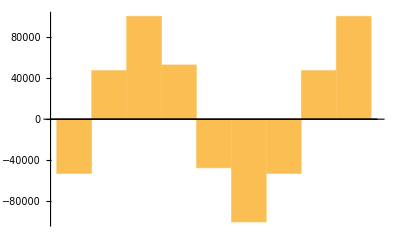

```mathematica
RectangleChart[Table[{10,100000Cos[(n π)/3-(400*0.000001)^2*π*500*1000/(0.0006*22*6)]},{n,1,9}]]
```

```mathematica
myPhaseFn[0.0006,500,0.022,0.0006]/(2π)*0.022/0.0006
```

250.

```mathematica
%/(2π)0.022
```

0.875352

```mathematica
D[myPhaseFn[t,vf,L,Δt],t]/(2π)*L/.t->Δt
```

vf

```mathematica
vOut = Import["vOut.dat"];

Mean[Last/@vOut]
Max[#]-Min[#]& @ (Last/@vOut)
StandardDeviation[Last/@vOut]
Mean[Length/@vOut]//N
```

539.61

326.129

61.721

484.455

```mathematica
500*0.00045/(6*0.022)//Rationalize
```

75/44

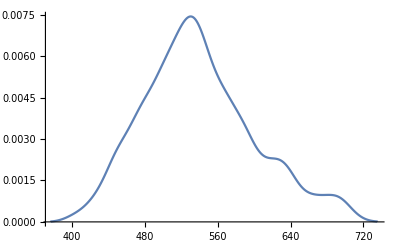

```mathematica
SmoothHistogram[Last/@vOut]
```

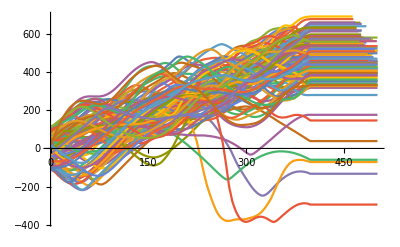

```mathematica
vOutS = Import["vOutS.dat"];
ListLinePlot[vOutS]
```

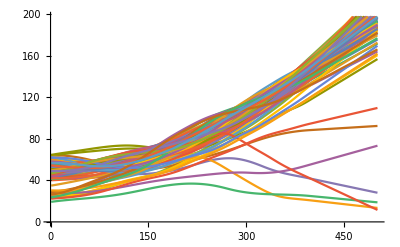

```mathematica
zOutS = Import["zOutS.dat"];
ListLinePlot[zOutS]
```

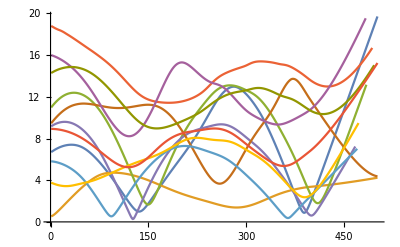

```mathematica
rOutS  = Import["rOutS.dat"];
ListLinePlot[rOutS[[20;;30]]]
```

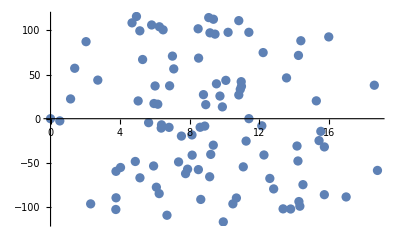

```mathematica
ListPlot[Transpose[{First/@rOutS,First/@vOutS}]]
```

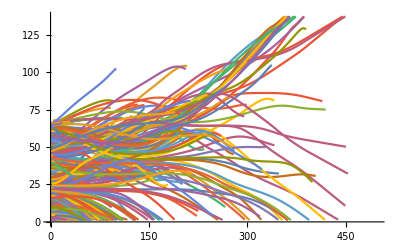

```mathematica
zOutC = Import["zOutC.dat"];
ListLinePlot[zOutC]
```

```mathematica
ListLinePlot[MapThread[Transpose[{#1,#2}]&,{zOutS,rOutS}][[20]]]
```

MapThread::mptd: Object zOutS at position {2, 1} in MapThread[Transpose[{#1, #2}] &, {zOutS, rOutS}] has only 0 of required 1 dimensions.

Part::partw: Part 20 of MapThread[Transpose[{#1, #2}] &, {zOutS, rOutS}] does not exist.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: MapThread[Transpose[{#1, #2}] &, {zOutS, rOutS}] ⟦ 20 ⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[MapThread[Transpose[{#1,#2}]&,{zOutS,rOutS}]⟦20⟧]

```mathematica
FileFormat["vOutS.dat"]
```

Table

```mathematica
mullerFac[x_,y_,z_]:=1/√(x^2+y^2+z^2)
rps = Table[{30*√(#[[1]])*Cos[#[[2]]],30*√(#[[1]])*Sin[#[[2]]],RandomReal[{10,40}]}&@{RandomReal[],RandomReal[{0,2π}]},{2000}];
rvs = Table[{#[[1]]*mullerFac[#[[2]],#[[3]],#[[4]]]*#[[2]],#[[1]]*mullerFac[#[[2]],#[[3]],#[[4]]]*#[[3]],#[[1]]*mullerFac[#[[2]],#[[3]],#[[4]]]*#[[4]]}&@
{100*(RandomReal[])^(1/3),RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]]},{2000}];
```

```mathematica
ListPointPlot3D[rvs,BoxRatios->Automatic]
```

-Graphics3D-

-Graphics3D-